### Dark Matter

```mathematica
(* Cosmological DM *)
```

```mathematica
1/2(m^2 ϕ^2)/(3 H^2 Mp^2)/.{H-> 2.1320 0.67 10^-42 10^9 eV,m-> 10^-20 10^9 eV,ϕ-> 4.5 10^-4  10^9 eV,Mp-> 2.435 10^18  10^9 eV}
```

0.278966

```mathematica
(* Galactic DM *)
```

```mathematica
GeVcm = 5.0676 10^13;
rhoDMgalaxy = 0.4 1/(GeVcm)^3 GeV^4;
```

```mathematica
Solve[1/2 m^2 ϕ1^2==rhoDMgalaxy,ϕ1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϕ1→-(2.47937×10^-21 GeV^2)/m},{ϕ1→(2.47937×10^-21 GeV^2)/m}}

```mathematica
ϕ1->(2.4793709150566806*^-21 GeV^2)/m/.{m-> 10^-20 10^9 eV,GeV-> 10^9 eV}
```

ϕ1→2.47937×10^8 eV

```mathematica
(* Occupataion number*)
```

```mathematica
l[m_,v_]:= (2π)/(m v); n[m_,v_]:=1/l[m,v]^3;
```

```mathematica
Solve[m  n[m,v]== rhoDMgalaxy ,m]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m→-(1.66168×10^-10 GeV)/v^(3/4)},{m→-((0.+1.66168×10^-10 ⅈ) GeV)/v^(3/4)},{m→((0.+1.66168×10^-10 ⅈ) GeV)/v^(3/4)},{m→(1.66168×10^-10 GeV)/v^(3/4)}}

```mathematica
m->(1.6616829108371048*^-10 GeV)/v^(3/4)/.{v-> 10^-3,GeV-> 10^9 eV}
```

m→29.5494 eV

## Plot

## Initial

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage[dvipsnames]{xcolor}"}];

tex[a_,b_]:=MaTeX[a,Magnification->b];
tex15[a_]:=MaTeX[a,Magnification->1.5];
```

```mathematica
(* BaseStyle->{FontFamily->"Latin Modern Math"} *) 
mysty={BaseStyle->{FontFamily->"Latin Modern Math",FontColor->Black},
FrameStyle->BlackFrame,
Frame->True,
Axes->False};

ticks=Flatten[
Join[Table[Join[{{10^j,StringForm["10^(``)",j],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-30,30}]],1];
ticksNoLabel=Flatten[
Join[Table[Join[{{10^j,StringForm["",j],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-30,30}]],1];

ticksEven=Flatten[
Join[Table[Join[{{10^j,If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];

ticksOdd=Flatten[
Join[Table[Join[{{10^j,If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];
ticksany[n_]:=Flatten[
Join[Table[Join[{{10^j,If[Mod[j,n]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-50,30}]],1];
Logticksany[n_]:=Flatten[
Join[Table[Join[{{Log[10,10^j],If[Mod[j,n]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-30,30}]],1];

Logticks=Flatten[
Join[Table[Join[{{Log[10,10^j],StringForm["10^(``)",j],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,20}]],1];

LogticksEven=Flatten[
Join[Table[Join[{{Log[10,10^j],If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,20}]],1];

LogticksOdd=Flatten[
Join[Table[Join[{{Log[10,10^j],If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,20}]],1];

Reverseticks=Flatten[
Join[Table[Join[{{10^-j,StringForm["10^(``)",j],{0.02,0}}},Table[{i^-1*10^-j,"",{0.008,0}},{i,2,9}]],{j,-20,20}]],1];

ReverseticksOdd=Flatten[
Join[Table[Join[{{10^-j,If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i^-1*10^-j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];

ReverseticksEven=Flatten[
Join[ Table[Join[{{10^-j,If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i^-1*10^-j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];
Reverseticksany[n_]:=Flatten[
Join[ Table[Join[{{10^-j,If[Mod[j,n]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i^-1*10^-j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];
```

## Theory

```mathematica
ClearAll;
```

```mathematica
eVs=1.5192 10^15;
G=1/MPl^2;
MPl=1.22 10^19. ;
Mpl = MPl/(√(8 π));
me0=0.511 ;  (* in MeV *)
ρDM=0.4/(((eVs 10^9)/(3 10^10.))^3); (* in GeV *)
me = 0.511 10^-3.;(* in GeV *)
```

## Existing ClockPlots

```mathematica
dir=NotebookDirectory[];
dir1 = "/Users/papai/Dropbox (Weizmann Institute)/CF2/untitled folder/";
```

```mathematica
framelabelgalphafphi={FrameLabel->{MaTeX["f_{\\phi}\\,\\,(\\rm Hz)",Magnification->1.5],MaTeX["g_{\\gamma}\\,\\,(\\rm eV^{-1})",Magnification->1.5]}};

framelabelgalphamphi={FrameLabel->{MaTeX["m_{\\phi}\\,\\,(\\rm eV)",Magnification->1.5],MaTeX["g_{\\gamma}\\,\\,(\\rm eV^{-1})",Magnification->1.5]}};

framelabeldemphi = {FrameLabel->{MaTeX["m_{\\phi}\\,\\,(\\rm eV)",Magnification->1.5],MaTeX["d_{e}",Magnification->1.5]}};
```

### Alpha Coupling

```mathematica
(* Stadnik 1807 *) 

destadnik = Import[dir1<>"dalphastadnik1807.csv"]; (* m vs de *)
dalphastadnikar =Array[Null,{Length[dalphastadnik],2}]; 
galphastadnikar = Array[Null,{Length[dalphastadnik],2}]; 

For[i=1,i<Length[destadnik]+1,i++,

dalphastadnikar[[i]][[1]]=destadnik[[i]][[1]]; (* mphi *)
dalphastadnikar[[i]][[2]]=destadnik[[i]][[2]]*1/(√2) ;(* dα*)

galphastadnikar[[i]][[1]]=destadnik[[i]][[1]]; (* mphi *)
galphastadnikar[[i]][[2]]=destadnik[[i]][[2]]*1/(√2 Mpl 10^9) ;(* dα*)
]//Quiet

dalphastadnikar= SortBy[dalphastadnikar,First];
galphastadnikar= SortBy[galphastadnikar,First];

(* Rb/Cs *)

rbcs = Import[dir1<>"RbCs.csv"]; (* de *)
dalpharbcs =Array[Null,{Length[rbcs],2}]; 
galpharbcs = Array[Null,{Length[rbcs],2}]; 

For[i=1,i<Length[rbcs]+1,i++,

dalpharbcs[[i]][[1]]=rbcs[[i]][[1]]; (* mphi *)
dalpharbcs[[i]][[2]]=rbcs[[i]][[2]]*1/(√2) ;(* dα*)

galpharbcs[[i]][[1]]=rbcs[[i]][[1]]; (* mphi *)
galpharbcs[[i]][[2]]=rbcs[[i]][[2]]*1/(√2 Mpl 10^9) ; (* gγ*)

]//Quiet

dalpharbcs = SortBy[dalpharbcs ,First];
galpharbcs= SortBy[galpharbcs,First];

(* Dy/Dy *)

dydy = Import[dir1<>"DyDy.csv"]; (* de *)
dalphadydy =Array[Null,{Length[dydy],2}]; 
galphadydy = Array[Null,{Length[dydy],2}]; 

For[i=1,i<Length[dydy]+1,i++,

dalphadydy[[i]][[1]]=dydy[[i]][[1]]; (* mphi *)
dalphadydy[[i]][[2]]=dydy[[i]][[2]]*1/(√2) ;(* dα*)

galphadydy[[i]][[1]]=dydy[[i]][[1]]; (* mphi *)
galphadydy[[i]][[2]]=dydy[[i]][[2]]*1/(√2 Mpl 10^9) ; (* gγ*)

]//Quiet

dydy2 = Import[dir1<>"DyDy2.csv"]; (* de *)
dalphadydy2 =Array[Null,{Length[dydy2],2}]; 
galphadydy2 = Array[Null,{Length[dydy2],2}]; 

For[i=1,i<Length[dydy2]+1,i++,

dalphadydy2[[i]][[1]]=dydy2[[i]][[1]]; (* mphi *)
dalphadydy2[[i]][[2]]=dydy2[[i]][[2]]*1/(√2) ;(* dα*)

galphadydy2[[i]][[1]]=dydy2[[i]][[1]]; (* mphi *)
galphadydy2[[i]][[2]]=dydy2[[i]][[2]]*1/(√2 Mpl 10^9) ; (* gγ*)

]//Quiet


(* GEO 600 - https://arxiv.org/pdf/2103.03783.pdf *)

geo600alpha=Import[dir1<>"geo600alpha.csv"]; (* Λα^-1 *)

geo600alphaar =Array[Null,{Length[geo600alpha],2}]; 
geo600alphaar2 =Array[Null,{Length[geo600alpha],2}];
geo600galphaar =Array[Null,{Length[geo600alpha],2}]; 
geo600de =Array[Null,{Length[geo600alpha],2}]; 

For[i=1,i<Length[geo600alpha]+1,i++,

geo600alphaar[[i]][[1]]=geo600alpha[[i]][[1]]; (* m *)
geo600alphaar[[i]][[2]]=geo600alpha[[i]][[2]]*Mpl; (* dα*)

geo600de[[i]][[1]]=geo600alpha[[i]][[1]]; (* m *)
geo600de[[i]][[2]]=geo600alpha[[i]][[2]]*√2 Mpl; (* de*)

geo600alphaar2[[i]][[1]]=eVs/(2π) geo600alpha[[i]][[1]]; (* f *)
geo600alphaar2[[i]][[2]]=geo600alpha[[i]][[2]]*Mpl;(* dα *)

geo600galphaar[[i]][[1]]=geo600alpha[[i]][[1]]; (* m *)
geo600galphaar[[i]][[2]]=geo600alpha[[i]][[2]]*10^-9.; (* gγ*)


]//Quiet

(* https://arxiv.org/pdf/2006.07055.pdf *) (* de *)

savallefde=Import[dir1<>"savallealpha.csv"]; 
savallealphaar =Array[Null,{Length[savallefde],2}];
savallealphaar2 =Array[Null,{Length[savallefde],2}]; 
savallegalphaar = Array[Null,{Length[savallefde],2}]; 
savallemde = Array[Null,{Length[savallefde],2}]; 

For[i=1,i<Length[savallefde]+1,i++,

savallealphaar[[i]][[1]]=(2π)/eVs savallefde[[i]][[1]]; (* m *)
savallealphaar[[i]][[2]]=savallefde[[i]][[2]]*1/(√2); (* dα *)
savallemde[[i]][[1]]=(2π)/eVs savallefde[[i]][[1]]; (* m *)
savallemde[[i]][[2]]=savallefde[[i]][[2]]; (* de *)

savallealphaar2[[i]][[1]]=savallefde[[i]][[1]]; (* f *)
savallealphaar2[[i]][[2]]=savallefde[[i]][[2]]*1/(√2) ;(* dα *)
savallegalphaar[[i]][[1]]=(2π)/eVs savallefde[[i]][[1]]; (* m *)
savallegalphaar[[i]][[2]]=savallefde[[i]][[2]]*1/(√2 Mpl 10^9.); (* gα *)


]//Quiet
savallealphaar= SortBy[savallealphaar,First];
savallealphaar2= SortBy[savallealphaar2,First];
savallegalphaar= SortBy[savallegalphaar,First];

(* https://arxiv.org/abs/1902.02788.pdf *)
DDalpha=Import[dir1<>"DDalpha.csv"]; 
DDalphaar =Array[Null,{Length[DDalpha],2}]; 
DDalphaar2 =Array[Null,{Length[DDalpha],2}]; 
DDde=Array[Null,{Length[DDalpha],2}]; 

For[i=1,i<Length[DDalpha]+1,i++,

DDalphaar[[i]][[1]]=DDalpha[[i]][[1]];(* m *)
DDalphaar[[i]][[2]]=DDalpha[[i]][[2]]*10^9.*Mpl; (* dα *)

DDde[[i]][[1]]=DDalpha[[i]][[1]];(* m *)
DDde[[i]][[2]]=DDalpha[[i]][[2]]*10^9.*√2 Mpl; (* dα *)

DDalphaar2[[i]][[1]]=eVs/(2π)DDalpha[[i]][[1]];(* f *)
DDalphaar2[[i]][[2]]=DDalpha[[i]][[2]]*10^9.*Mpl (* dα *)
]//Quiet

(* WRESL1, 1905.02968 and 2012.01519 *)

WRESLalpha = Import[dir1<>"WRESLfdf.csv"];
WRESLalphaar =Array[Null,{Length[WRESLalpha],2}];
WRESLalphaar2 =Array[Null,{Length[WRESLalpha],2}];
WRESLgalphaar = Array[Null,{Length[WRESLalpha],2}];
WRESLde = Array[Null,{Length[WRESLalpha],2}];

For[i=1,i<Length[WRESLalpha]+1,i++,
WRESLalphaar[[i]][[1]]=(2π)/eVs WRESLalpha[[i]][[1]];(*m *)
WRESLalphaar[[i]][[2]]=WRESLalpha[[i]][[2]] (Mpl(2π)/eVs WRESLalpha[[i]][[1]] 10^-9.)/(√(2 ρDM))*If[WRESLalpha[[i]][[1]]>= 50 10^3,1/2,1];(* dα *)

WRESLde[[i]][[1]]=(2π)/eVs WRESLalpha[[i]][[1]];(*m *)
WRESLde[[i]][[2]]=WRESLalpha[[i]][[2]] (√2 Mpl(2π)/eVs WRESLalpha[[i]][[1]] 10^-9.)/(√(2 ρDM))*If[WRESLalpha[[i]][[1]]>= 50 10^3,1/2,1];(* de *)

WRESLalphaar2[[i]][[1]]= WRESLalpha[[i]][[1]];(*f *)
WRESLalphaar2[[i]][[2]]=WRESLalpha[[i]][[2]] (Mpl(2π)/eVs WRESLalpha[[i]][[1]] 10^-9.)/(√(2 ρDM))*If[WRESLalpha[[i]][[1]]>= 50 10^3,1/2,1];(* dα *)

WRESLgalphaar[[i]][[1]]=(2π)/eVs WRESLalpha[[i]][[1]];(* m *)
WRESLgalphaar[[i]][[2]]=WRESLalpha[[i]][[2]] ((2π)/eVs WRESLalpha[[i]][[1]] 10^-9.)/(√(2 ρDM)10^9.)*If[WRESLalpha[[i]][[1]]>= 50 10^3,1/2,1];(* gγ ev^-1 *)

]//Quiet


(* Fermilab Holometer, https://arxiv.org/pdf/2108.04746.pdf *)

holometeralpha=Import[dir1<>"Holometergamma.csv"]; (* Λα^-1 *)

holometeralphaar =Array[Null,{Length[holometeralpha],2}]; 
holometeralphaar2 =Array[Null,{Length[holometeralpha],2}];
holometergalphaar =Array[Null,{Length[holometeralpha],2}]; 
holometerde =Array[Null,{Length[holometeralpha],2}]; 

For[i=1,i<Length[holometeralpha]+1,i++,

holometeralphaar[[i]][[1]]=holometeralpha[[i]][[1]]; (* m *)
holometeralphaar[[i]][[2]]=holometeralpha[[i]][[2]]*Mpl; (* dα*)

holometerde[[i]][[1]]=holometeralpha[[i]][[1]]; (* m *)
holometerde[[i]][[2]]=holometeralpha[[i]][[2]]*√2 Mpl; (* de*)

holometeralphaar2[[i]][[1]]=eVs/(2π) holometeralpha[[i]][[1]];(*f*)  
holometeralphaar2[[i]][[2]]=holometeralpha[[i]][[2]]*Mpl;(* dα *)

holometergalphaar[[i]][[1]]=holometeralpha[[i]][[1]]; (* m *)
holometergalphaar[[i]][[2]]=holometeralpha[[i]][[2]]*10^-9.; (* gγ ev^-1 *)


]//Quiet

(* Molecular Ensemble *)

moliodinedalpha=Import[dir1<>"moliodinealpha.csv"]; (* dalpha *)

moliodinefggamma = Array[Null,{Length[moliodinedalpha],2}];
moliodinemggamma = Array[Null,{Length[moliodinedalpha],2}];
moliodinede = Array[Null,{Length[moliodinedalpha],2}];

For[i=1,i<= Length[moliodinedalpha],i++,

moliodinede[[i]][[1]] = (2 π)/eVs moliodinedalpha[[i]][[1]];(* m *)
moliodinede[[i]][[2]] =  moliodinedalpha[[i]][[2]] √2;(* de *)


moliodinefggamma[[i]][[1]]= moliodinedalpha[[i]][[1]];(* f *)
moliodinefggamma[[i]][[2]]= moliodinedalpha[[i]][[2]] 1/(Mpl 10^9);(* gγ *)

moliodinemggamma[[i]][[1]] = (2 π)/eVs moliodinedalpha[[i]][[1]];(* m *)
moliodinemggamma[[i]][[2]] =  moliodinedalpha[[i]][[2]] 1/(Mpl 10^9)(* gγ *)
]//Quiet

(* AUriga *)(* de with √(4PiG)*)

auriga = Import[dir1<>"Auriga.csv"]; 
aurigaarf = Array[Null,{Length[auriga],2}];
aurigaarmgalpha = Array[Null,{Length[auriga],2}];

For[i=1,i<Length[auriga]+1,i++,
aurigaarf[[i]][[1]]= auriga[[i]][[1]] eVs/(2π);
aurigaarf[[i]][[2]]= auriga[[i]][[2]];

aurigaarmgalpha[[i]][[1]]= auriga[[i]][[1]];
aurigaarmgalpha[[i]][[2]]= auriga[[i]][[2]] 1/(√2 Mpl 10^9);
]

(* WRESL 2 *)
incohnataniel = Import[dir1<>"WRESL2data.csv"];
natfalpha = Array[Null,{Length[incohnataniel],2}];
natfdalpha = Array[Null,{Length[incohnataniel],2}];

natmdalpha = Array[Null,{Length[incohnataniel],2}];
natmalpha=Array[Null,{Length[incohnataniel],2}];
natde = Array[Null,{Length[incohnataniel],2}];

For[i=1, i<Length[incohnataniel]+1,i++,

natmdalpha[[i]][[1]]= (2 π)/eVs incohnataniel[[i]][[1]] ;(* m eV *)
natmdalpha[[i]][[2]] =incohnataniel[[i]][[2]]((2 π)/eVs incohnataniel[[i]][[1]](Mpl*10^9))/(√(2 ρDM)*10^18.)*If[incohnataniel[[i]][[1]]>=50 10^3.,1/2.2577565632458234,1/1.2577565632458234] ;(* dα *)


natde[[i]][[1]]= (2 π)/eVs incohnataniel[[i]][[1]] ;(* m eV *)
natde[[i]][[2]] =incohnataniel[[i]][[2]]((2 π)/eVs incohnataniel[[i]][[1]](√2 Mpl* 10^9))/(√(2 ρDM)*10^18.)*If[incohnataniel[[i]][[1]]>=50 10^3.,1/2.2577565632458234,1/1.2577565632458234] ;(* de *)


natmalpha[[i]][[1]]= (2 π)/eVs incohnataniel[[i]][[1]] ;(* m eV *)
natmalpha[[i]][[2]] =incohnataniel[[i]][[2]]((2 π)/eVs incohnataniel[[i]][[1]])/(√(2 ρDM)*10^18.)*If[incohnataniel[[i]][[1]]>=50 10^3.,1/2.2577565632458234,1/1.2577565632458234] ;(* gγ *)


natfdalpha[[i]][[1]]= incohnataniel[[i]][[1]] ;(* f Hz *)
natfdalpha[[i]][[2]] =incohnataniel[[i]][[2]]((2 π)/eVs incohnataniel[[i]][[1]](Mpl* 10^9))/(√(2 ρDM)*10^18.)*If[incohnataniel[[i]][[1]]>=50 10^3.,1/2.2577565632458234,1/1.2577565632458234] ;(* dα *)


natfalpha[[i]][[1]]= incohnataniel[[i]][[1]] ;(* f Hz *)
natfalpha[[i]][[2]] =incohnataniel[[i]][[2]]((2 π)/eVs incohnataniel[[i]][[1]])/(√(2 ρDM)*10^18.)*If[incohnataniel[[i]][[1]]>=50 10^3.,1/2.2577565632458234,1/1.2577565632458234] ;(* gγ *)

] //Quiet

geo600alpha=Import[dir1<>"geo600alpha.csv"]; (* Λα^-1 *)
(* https://arxiv.org/pdf/2103.03783.pdf *)

geo600alphaar =Array[Null,{Length[geo600alpha],2}]; 
geo600alphaar2 =Array[Null,{Length[geo600alpha],2}];
geo600mgalpha =Array[Null,{Length[geo600alpha],2}];
geo600de=Array[Null,{Length[geo600alpha],2}];

For[i=1,i<Length[geo600alpha]+1,i++,

geo600alphaar[[i]][[1]]=geo600alpha[[i]][[1]]; (* m *)
geo600alphaar[[i]][[2]]=geo600alpha[[i]][[2]]*Mpl; (* dα*)

geo600de[[i]][[1]]=geo600alpha[[i]][[1]]; (* m *)
geo600de[[i]][[2]]=geo600alpha[[i]][[2]]*√2 Mpl; (* de*)

geo600mgalpha[[i]][[1]]=geo600alpha[[i]][[1]]; (* m *)
geo600mgalpha[[i]][[2]]=geo600alpha[[i]][[2]] 1/10^9;(* gγ *)

geo600alphaar2[[i]][[1]]=eVs/(2π) geo600alpha[[i]][[1]]; (* f *)
geo600alphaar2[[i]][[2]]=geo600alpha[[i]][[2]]*Mpl(* dα *)
]//Quiet

(* https://journals.aps.org/prl/pdf/10.1103/PhysRevLett.126.071301 *)
campbell = Import[dir1<>"campbell.csv"]; (* de, √(4PiG) *)

junyehsi=Import[dir1<>"kennedyhsi.csv"]; (* de, √(4PiG) *)(*  https://journals.aps.org/prl/pdf/10.1103/PhysRevLett.125.201302  *)

junyehsimgalpha =Array[Null,{Length[junyehsi],2}]; 
junyehsifgalpha =Array[Null,{Length[junyehsi],2}];

For[i=1,i<Length[junyehsi]+1,i++,

junyehsimgalpha[[i]][[1]]=junyehsi[[i]][[1]]; (* m *)
junyehsimgalpha[[i]][[2]]=junyehsi[[i]][[2]] 1/(√2 Mpl 10^9);(* gγ *)

junyehsifgalpha[[i]][[1]]=eVs/(2π) junyehsi[[i]][[1]]; (* f *)
junyehsifgalpha[[i]][[2]]=junyehsi[[i]][[2]] 1/(√2 Mpl 10^9)(* gγ *)
]//Quiet

junyesrsi=Import[dir1<>"kennedysrsi.csv"]; (* de *)(*  https://journals.aps.org/prl/pdf/10.1103/PhysRevLett.125.201302  *)

junyesrsimgalpha =Array[Null,{Length[junyesrsi],2}]; 
junyesrsifgalpha =Array[Null,{Length[junyehsi],2}];

For[i=1,i<Length[junyesrsi]+1,i++,

junyesrsimgalpha[[i]][[1]]=junyesrsi[[i]][[1]]; (* m *)
junyesrsimgalpha[[i]][[2]]=junyesrsi[[i]][[2]] 1/(√2 Mpl 10^9);(* gγ *)

junyesrsifgalpha[[i]][[1]]=eVs/(2π) junyesrsi[[i]][[1]]; (* f *)
junyesrsifgalpha[[i]][[2]]=junyesrsi[[i]][[2]] 1/(√2 Mpl 10^9)(* gγ *)
]//Quiet

(* https://www.nature.com/articles/s41586-021-03253-4 *)
(*junyealhg=Import[dir1<>"junyeAlHg.csv"]; (* de *)
junyealyb=Import[dir1<>"junyeAlYb.csv"]; (* de *) 
junyeybsr=Import[dir1<>"junyeYbSr.csv"]; (* de *) *)

junyealybhgsr=Import[dir1<>"junyealybhgsr.csv"]; (* de *) 

(* MAGIS *)
magis100 = Import[dir1<>"magis100.csv"];
magiskm = Import[dir1<>"magiskm.csv"];
```

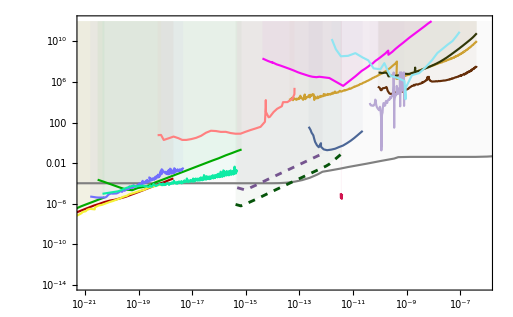

```mathematica
clkpltsalpha= ListLogLogPlot[{SortBy[destadnik,First],
SortBy[dydy,First],SortBy[dydy2,First],SortBy[rbcs,First],
moliodinede,WRESLde,SortBy[natde,First],
geo600de,SortBy[DDde,First],
SortBy[savallemde,First], 
SortBy[holometerde,First],auriga,
SortBy[junyealybhgsr,First],
junyehsi,junyesrsi,SortBy[magis100,First],SortBy[magiskm,First],SortBy[campbell,First]
},PlotRange->{{ 10^-21,8 10^-7},{10^-14,10^12}},
FrameTicks->{
{ticksany[3],ticksNoLabel},
{ticksany[3],ticksNoLabel}},
PlotStyle->{
Directive[Thickness[0.003],Gray,Line],
Directive[Thickness[0.003],Darker[Green],Line],
Directive[Thickness[0.003],Darker[Green],Line],
Directive[Thickness[0.003],Darker[Red],Line],
Directive[Thickness[0.003],colorTable[[3]],Line],
Directive[Thickness[0.003],colorTable[[24]],Line],
Directive[Thickness[0.003],colorTable[[28]],Line],
Directive[Thickness[0.003],colorTable[[6]],Line],
Directive[Thickness[0.003],colorTable[[7]],Line],
Directive[Thickness[0.003],colorTable[[8]],Line],
Directive[Thickness[0.003],colorTable[[9]],Line],
Directive[Thickness[0.003],colorTable[[23]],Line],
Directive[Thickness[0.003],colorTable[[11]],Line],
Directive[Thickness[0.003],colorTable[[12]],Line],
Directive[Thickness[0.003],colorTable[[13]],Line],
Directive[Thickness[0.004],colorTable[[20]],Dashed],
Directive[Thickness[0.004],colorTable[[15]],Dashed],
Directive[Thickness[0.003],Pink,Line]
},
FrameTicksStyle->{{Thin,Thin},{Thin,Thin}},
Filling->Top,
Joined->True,
(*GridLines->All,*)
FillingStyle->Opacity[0.04],#1,#2]&[mysty,framelabeldemphi]
```

### Nuclear Clock Projection

```mathematica
taucoh[mphi_]:=  (2 Pi 10^6)/(mphi*eVs);

F1[Tint_,mphi_]:=If[Tint≤ taucoh[mphi],√Tint,(Tint*taucoh[mphi])^(1/4) ];
Tavg=1;
sigmay[T_]:=(8 10^-17.)/(√(T*Tavg));

(* Nuclear clock sensitivity for α *)

galphanclclk[mphi_,Tint_,T_]:= (10^-4.*sigmay[T]/F1[Tint,mphi]*mphi/(√(2*ρDM*10^36.))*Abs[(mphi*eVs*Tavg)/Sin[mphi*eVs*Tavg]])//Simplify ;

denclclk[mphi_,Tint_,T_]:= (10^-4.*sigmay[T]/F1[Tint,mphi]*(mphi (√2 Mpl 10^9))/(√(2*ρDM*10^36.))*Abs[(mphi*eVs*Tavg)/Sin[mphi*eVs*Tavg]])//Simplify ;

galphanclclkfit[mphi_,Tint_,T_]:= If[mphi≤ 1.1 10^-15, galphanclclk[mphi,Tint,T], galphanclclk[ 1.1 10^-15,Tint,T]*(mphi/(1.1 10^-15))^(9/4)];
denclclkfit[mphi_,Tint_,T_]:= If[mphi≤ 1.1 10^-15,denclclk[mphi,Tint,T], denclclk[ 1.1 10^-15,Tint,T]*(mphi/(1.1 10^-15))^(9/4)];
```

```mathematica
nuclearplt[T_] :=  LogLogPlot[{(*galphanclclk[mphi,10^6,T],*)denclclkfit[(2Pi)/eVs fphi,10^6,T]},{fphi,eVs/(2Pi) 10^-21,eVs/(2Pi) 10^-6},
PlotRange->{{eVs/(2Pi) 10^-21,eVs/(2Pi) 10^-6},{10^-14,10^10}},
PlotStyle->{Directive[Dashed,Thickness[0.003],Darker[Red]](*,
Directive[Line,Thickness[0.002],Darker[Black]]*)},
PlotPoints-> 1000,
FrameTicks->{
{ticksany[3],Automatic},
{ticksEven,Automatic}},
#1,#2]&[mysty,framelabeldemphi];
```

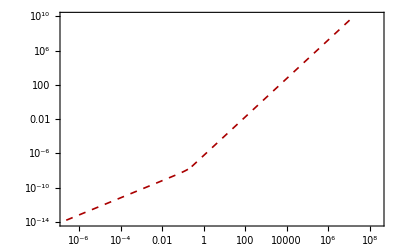

```mathematica
nuclearplt[0.5]
```

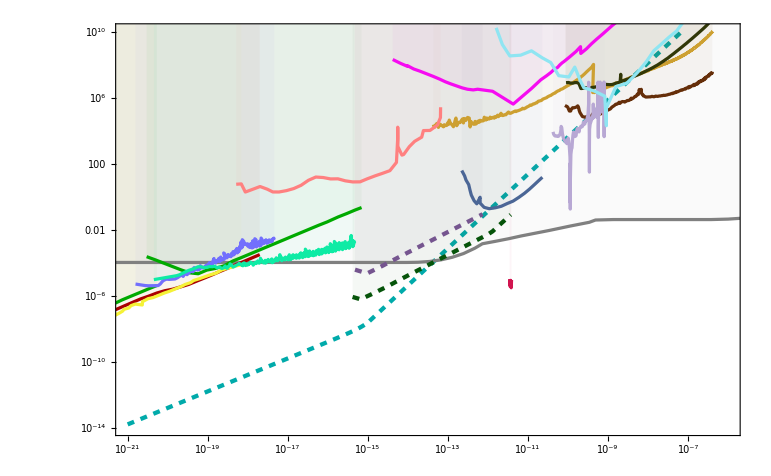

```mathematica
Show[LogLogPlot[{(*galphanclclk[mphi,10^6,T],*)denclclkfit[mphi,10^6,0.5]},{mphi, 10^-21,10^-6},
PlotRange->{{ 10^-21,10^-6},{10^-14,10^10}},
PlotStyle->{Directive[Dashed,Thickness[0.004],Darker[Cyan]](*,
Directive[Line,Thickness[0.002],Darker[Black]]*)},
PlotPoints-> 1000,
FrameTicks->{
{ticksany[3],Automatic},
{ticksany[3],Automatic}},
#1,#2]&[mysty,framelabeldemphi],clkpltsalpha]
```

### Plot with two different x axes

```mathematica
PacletInstall["GraphicsInformation","Site"->"http://raw.githubusercontent.com/carlwoll/GraphicsInformation/master"];
<<GraphicsInformation`
```

```mathematica
framelabel1={FrameLabel->{MaTeX["m_\\phi\\,\\,(\\rm eV)",Magnification->1.5],None,MaTeX["f\\,\\,(\\rm Hz)",Magnification->1.5]}};
framelabel2={FrameLabel->{None,MaTeX["g_{\\gamma}\\,\\,(\\rm eV^{-1})",Magnification->1.5] }};
framelabel4={FrameLabel->{None,MaTeX["d_{e}",Magnification->1.5] }};
```

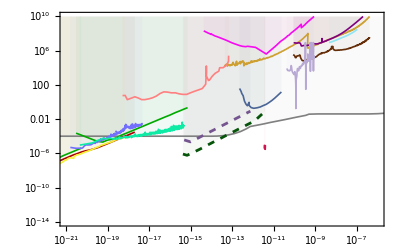
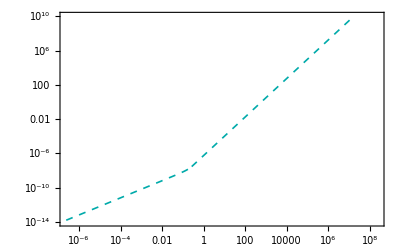

```mathematica
pltsfinal= {
ListLogLogPlot[{SortBy[destadnik,First],
SortBy[dydy,First],SortBy[dydy2,First],SortBy[rbcs,First],
moliodinede,WRESLde,SortBy[natde,First],
geo600de,SortBy[DDde,First],
SortBy[savallemde,First], 
holometerde,auriga,
SortBy[junyealybhgsr,First],
junyehsi,junyesrsi,SortBy[magis100,First],SortBy[magiskm,First],SortBy[campbell,First]
},PlotRange->{{ 10^-21,10^-6},{10^-14,10^10}},
FrameTicks->{
{None,Automatic},
{ticksany[3],Automatic}},
PlotStyle->{
Directive[Thickness[0.003],Gray,Line],
Directive[Thickness[0.003],Darker[Green],Line],
Directive[Thickness[0.003],Darker[Green],Line],
Directive[Thickness[0.003],Darker[Red],Line],
Directive[Thickness[0.003],colorTable[[3]],Line],
Directive[Thickness[0.003],Purple,Line],
Directive[Thickness[0.003],colorTable[[28]],Line],
Directive[Thickness[0.003],colorTable[[6]],Line],
Directive[Thickness[0.003],colorTable[[7]],Line],
Directive[Thickness[0.003],colorTable[[8]],Line],
Directive[Thickness[0.003],colorTable[[9]],Line],
Directive[Thickness[0.003],colorTable[[23]],Line],
Directive[Thickness[0.003],colorTable[[11]],Line],
Directive[Thickness[0.003],colorTable[[12]],Line],
Directive[Thickness[0.003],colorTable[[13]],Line],
Directive[Thickness[0.005],colorTable[[20]],Dashed],
Directive[Thickness[0.005],colorTable[[15]],Dashed],
Directive[Thickness[0.003],Pink,Line]
},
FrameTicksStyle->{{Thin,Thin},{Thin,Thin}},
Filling->Top,
Joined->True,
(*GridLines->All,*)
FillingStyle->Opacity[0.04],#1,#2]&[mysty,framelabel1],
LogLogPlot[{(*galphanclclk[mphi,10^6,T],*)denclclkfit[(2Pi)/eVs fphi,10^6,0.5]},{fphi,eVs/(2Pi) 10^-21,eVs/(2Pi) 10^-6},
PlotRange->{{eVs/(2Pi) 10^-21,eVs/(2Pi) 10^-6},{10^-14,10^10}},
PlotStyle->{Directive[Dashed,Thickness[0.003],Darker[Cyan]](*,
Directive[Line,Thickness[0.002],Darker[Black]]*)},
PlotPoints-> 1000,
FrameTicks->{
{ticksany[4],Automatic},
{None,ticksEven}},
#1,#2]&[mysty,framelabel4]
};
padding="ImagePadding"/. GraphicsInformation[pltsfinal];

imagefinal= Overlay[{Show[pltsfinal[[1]],ImagePadding-> MapThread[Max,padding,2]],Show[pltsfinal[[2]],ImagePadding-> MapThread[Max,padding,2]]
}]
Export[dir<>"de_1.pdf",imagefinal,"PDF"];
```

```mathematica
a = {{1,2},{3,5}};b = {{8,9},{10,1}};
```

```mathematica
a+b
```

{{9,11},{13,6}}

```mathematica
AppendTo[a,Flatten[b]]
```

{{1,2},{3,5},{8,9,10,1}}

```mathematica
Flatten[{{1,2},{3,5},{{8,9},{10,1}}}]
```

{1,2,3,5,8,9,10,1}

```mathematica
destadnik[[1]]
```

{1.55506×10^-25,0.000102865}

```mathematica
0.00010286488651599578
```

0.000102865

```mathematica
ScientificForm[0.00010286488651599578]
```

1.02865×10^-4

```mathematica
destadnik[[1]]
```

{1.55506×10^-25,0.000102865}

```mathematica
√2 dEP[ηMicro,mphi,ΔQmicro,Qsi,QFe,0,Pi/2,0,0,1.11 Rearth]/.{mphi-> 10^-21}
```

0.000120845

```mathematica
ScientificForm[0.00012084518445346258]
```

1.20845×10^-4

```mathematica
ScientificForm[0.00008545044940078254]
```

8.54504×10^-5

```mathematica
4.125845181431949*^-9 √2
```

5.83483×10^-9

```mathematica
rbcs
```

{{4.85484×10^-25,7.07818×10^-8},{7.96041×10^-25,4.35837×10^-8},{1.30526×10^-24,2.64474×10^-8},{2.14021×10^-24,1.63325×10^-8},{3.50927×10^-24,1.00567×10^-8},{5.75409×10^-24,6.41329×10^-9},{9.43489×10^-24,4.38687×10^-9},{1.54702×10^-23,4.12585×10^-9},{2.53663×10^-23,5.97906×10^-9},{3.63452×10^-23,1.03851×10^-8},{5.20758×10^-23,2.00382×10^-8},{8.53878×10^-23,2.98125×10^-8},{1.40009×10^-22,4.15935×10^-8},{2.29571×10^-22,7.54801×10^-8},{3.76424×10^-22,1.10304×10^-7},{6.15369×10^-22,1.68577×10^-7},{9.73784×10^-22,2.99731×10^-7},{1.65942×10^-21,4.82026×10^-7},{2.66794×10^-21,7.4105×10^-7},{4.40453×10^-21,1.23811×10^-6},{7.34074×10^-21,1.75343×10^-6},{1.22464×10^-20,2.25067×10^-6},{2.05107×10^-20,3.19281×10^-6},{3.27606×10^-20,4.28874×10^-6},{5.28785×10^-20,6.73599×10^-6},{8.68899×10^-20,0.0000107832},{1.42167×10^-19,0.0000180014},{2.3311×10^-19,0.0000276567},{3.74571×10^-19,0.0000478271},{6.2673×10^-19,0.0000843465},{1.03459×10^-18,0.0001433},{1.72762×10^-18,0.00023328},{2.36063×10^-18,0.000321445}}

```mathematica
colorTable = Table[RandomColor[],30];
```

{RGBColor[0.2798822029618604, 0.8069129050838451, 0.13268898684822883],RGBColor[0.06220120114640615, 0.6947825900356299, 0.6714865314268654],RGBColor[0.8050694156258507, 0.6271991379346797, 0.19267429643414768],RGBColor[0.8292242635507492, 0.5382164192565355, 0.7549520568093884],RGBColor[0.20207568861108416, 0.21158739266749516, 0.5599916656041353],RGBColor[0.29552317650902404, 0.400499569338461, 0.5866259737157389],RGBColor[0.9655902021469629, 0.04190557829598829, 0.943776331944659],RGBColor[0.7201207701041699, 0.6580611611277696, 0.8304515177930007],RGBColor[0.5617428587715156, 0.899221712001607, 0.9505782817168908],RGBColor[0.9331345870187362, 0.4177429368388119, 0.8880914116728036],RGBColor[0.9614546172929275, 0.9507248025982635, 0.20993533186227276],RGBColor[0.4478355191820913, 0.4360801171884874, 0.9911060627194148],RGBColor[0.05732360943039727, 0.9221302287966864, 0.646359873870711],RGBColor[0.09787215639391511, 0.6104115678031208, 0.5576694113869194],RGBColor[0.023134181294280243, 0.330618777593896, 0.04024946996211787],RGBColor[0.09601349303690987, 0.012401874533843227, 0.12802822852662854],RGBColor[0.8118857075739474, 0.9664373860236013, 0.3130017140966379],RGBColor[0.3627369576587829, 0.4656932869723014, 0.3829303317608499],RGBColor[0.2335526400308301, 0.5374762267992466, 0.862234360546474],RGBColor[0.45772305959107973, 0.3314034431546755, 0.5604955134550009],RGBColor[0.2331061374455814, 0.3357398326055614, 0.7770424238709743],RGBColor[0.2498583405378061, 0.39227318460244986, 0.7068069466835247],RGBColor[0.8207855568083702, 0.0803689349310659, 0.31103762516754796],RGBColor[0.19162227812830968, 0.21701835833324634, 0.031425360619489195],RGBColor[0.4289296666977347, 0.9038663717605919, 0.005711427712237649],RGBColor[0.27662616706971344, 0.8984865138821494, 0.04162404052019664],RGBColor[0.7775152544698791, 0.7801744363118968, 0.34023724618604945],RGBColor[0.3969189164513445, 0.18090630497239513, 0.036403424705467646],RGBColor[0.9557840557433857, 0.03735952835822176, 0.7155059865272901],RGBColor[0.5393029784611199, 0.9757122572607471, 0.5001906370775029]}

```mathematica
colorTable[[4]]
```

RGBColor[0.8292242635507492, 0.5382164192565355, 0.7549520568093884]

```mathematica
ColorData[89][1]
```

Hue[0.5, 0.5, 0.4]

```mathematica
ColorData[89][2]
```

Hue[0.08, 0.9, 0.8]

```mathematica
ColorData[89][3]
```

Hue[0.42, 0.67, 0.6]

```mathematica
ColorData[89][4]
```

Hue[0.13, 0.8, 0.85]

```mathematica
ColorData[89][5]
```

Hue[0.5, 0.67, 0.6]

```mathematica
ColorData[89][6]
```

Hue[0.17, 0.9, 0.6]

```mathematica
ColorData[89][7]
```

Hue[0.67, 0.5, 0.7]

```mathematica
ColorData[89][8]
```

Hue[0.1, 0.75, 0.8]

```mathematica
ColorData[89][9]
```

Hue[0, 0.75, 0.8]

```mathematica
ColorData[89][9]
```

Hue[0.04, 0.8, 1]

```mathematica
ColorData[89][10]
```

Hue[0.04, 0.8, 1]

```mathematica
ColorData[89][11]
```

Hue[0.5, 0.5, 0.4]

```mathematica
gγ = de *√(4 Pi) 1/(MPl 10^9)
```

2.90566×10^-28 de

```mathematica
1/Λγ= gγ = √(4 Pi) de/MPl (* α *)
```

```mathematica
1/Λe me= ge  =√(4 Pi) (dme me)/MPl (* electron mass *);
(* In my notation MPl = √(8π)Mpl, so everything is consistent! *)
{MPl,Mpl}
```

Set::write: Tag Times in 0.000511/Λe is Protected.

{1.22×10^19,2.43355×10^18}